## Решение уравнения y' (x) =( x^2 y(x)^2 - (2 x + 1) y(x) + 1. ) / x, при начальном условии y(1)= 0, на интервале [ 1., 1.5 ] , с постоянным шагом h= 0.1 методами Эйлера, Рунге-Кутты и Адамса

```mathematica
ClearAll["y*"]
rt=NDSolve[ {y'[x]==  ( x^2 y[x]^2 -  (2 x + 1) y[x] + 1. ) / x, y[1.]==0.},
            y, {x,1.,1.5} ]
```

{{y→InterpolatingFunction[{{1.,1.5}},<>]}}

```mathematica
yt[x_]:=y[x]/.rt[[1]];  (*Функция решения,полученного с помощью встроенной функции. Будет использована для сравнения результатов  *)
```

### График решения

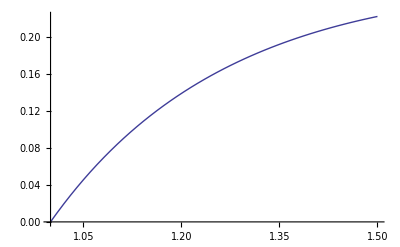

```mathematica
g1=Plot [ yt[x],{x,1.,1.5}] (*График решения,полученного с помощью встроенной функции *)
```

### Функция в правой части уравнения

```mathematica
f[x_,y_]:= ( x^2 y^2 -  (2 x + 1) y + 1. ) / x; (*Функция в правой части уравнения *)
```

## Вычисление решения по формулам Эйлера с постоянным шагом (с возможностью адаптации для автоматического выбора шага)

```mathematica
h=0.1;
a=1.;
b=1.5;
x0=a;
y0=0.;
X={x0};
yE={y0};
While[x0<b ,

     x1=x0+h;
     
     (* Вычисление значения решения в точке x1 *)
     
     y1 = y0 + h f[x0,y0]; 

     Print [" x= ", x1, "      y= ", y1];
     AppendTo[X,x1]; (* Добавление узла сетки *) 
     AppendTo[yE,y1]; (* Добавление значения решения в этом узле *)
     x0=x1;
     y0=y1;
];
```

x= 1.1      y= 0.1

x= 1.2      y= 0.162918

x= 1.3      y= 0.203276

x= 1.4      y= 0.229279

x= 1.5      y= 0.245835

## Сравнение решений, полученных по методу Эйлера и с помощью встроенной функции

{{1.,0.},{1.1,0.1},{1.2,0.162918},{1.3,0.203276},{1.4,0.229279},{1.5,0.245835}}

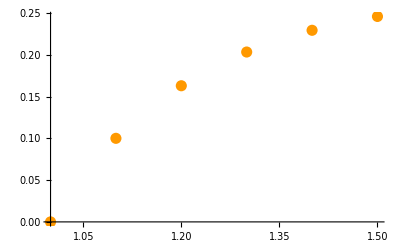

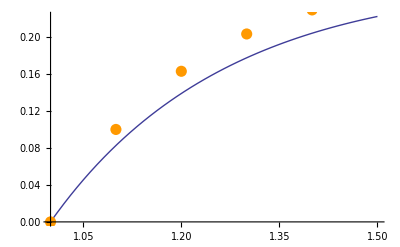

```mathematica
ynum=Transpose[{X,yE}]
g2=ListPlot[ynum,PlotStyle->{Hue[0.1],PointSize[0.02]}]
Show[g1,g2]
```

## Графическое изображение полученной интегральной кривой (ломанная Эйлера)

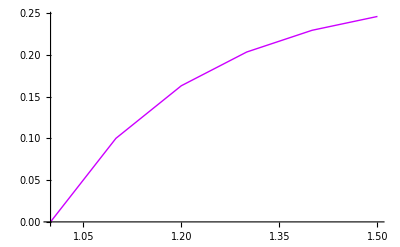

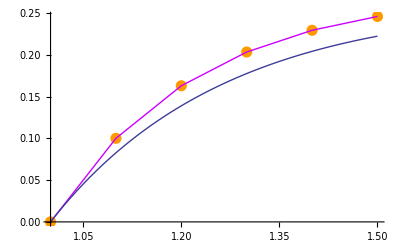

```mathematica
g3=ListPlot[ynum,Joined->True,PlotStyle->{Hue[0.8],PointSize[0.02]}] (*Ломанная Эйлера*)
Show[g2,g3,g1]
```

## Метод Рунге-Кутты 2 порядка с постоянным шагом (с возможностью адаптации для автоматического выбора шага)

```mathematica
h=0.1;
a=1.;
b=1.5;
x0=a;
y0=0.;
X=List[x0];
yR=List[y0];
While[x0<b ,

     x1=x0+h;
     
     (* Вычисление значения решения в точке x1 *)
     
     k1=h f[ x0 , y0 ];
     k2=h f[ x0+0.5 h , y0+0.5 k1 ];  
     y1 = y0 +k2;

     Print [" x= ", x1, "     y= ", y1];
     AppendTo[X,x1];
     AppendTo[yR,y1];
     x0=x1;
     y0=y1;
];
```

x= 1.1     y= 0.0807387

x= 1.2     y= 0.136266

x= 1.3     y= 0.174728

x= 1.4     y= 0.201383

x= 1.5     y= 0.219719

```mathematica
ynum=Transpose[{X,yR}]   (* Таблица значений функции решения, полученных в узлах сетки по методу Рунге-Кутты*)
```

{{1.,0.},{1.1,0.0807387},{1.2,0.136266},{1.3,0.174728},{1.4,0.201383},{1.5,0.219719}}

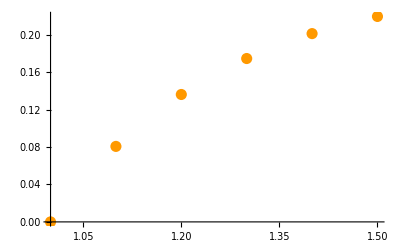

```mathematica
g2=ListPlot[ynum , PlotStyle->{Hue[0.1] , PointSize[0.02]} ]
```

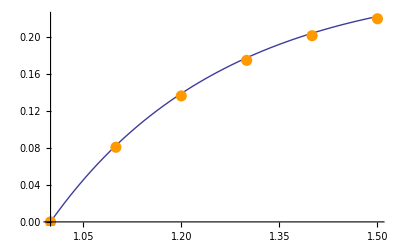

```mathematica
Show[g1,g2]
```

## Метод Адамса второго порядка точности p = 2. -явная формула - неявная формула

```mathematica
h=0.1;

b=1.5;
x0=1.;
y0=0.;
n=(b-x0)/h+1; (* Количество узлов сетки для заданого постоянного шага на  интервале решения задачи *)

 (* Массивы для размещения значений табличной функции решения *)
xA=Table [t,{t,x0,b,h}];
yA=Table[0,{n}] ;


(* Необходимые значения решения для начала вычислений по формулам Адамса *)

(* 
1 способ - использовать полученные в предыдущем пункте задания решения по методу Рунге-Кутты 
*)

yA[[1]]=yR[[1]];
yA[[2]]=yR[[2]];



(*
2 способ - получить значения решения в первых точках по методу Рунге-Куты,
             при этом для повышения точности вычислений использовать на этом этапе шаг в два раза меньший,
             чем для остальных вычислений 



yA[[1]]=y0;

  k1=h/2 f[ x0 , y0 ];
  k2=h/2 f[ x0+0.5 h/2 , y0+0.5 k1 ];  
  yp = y0 +k2;

 k1=h/2 f[ x0+h/2 , yp ];  
 k2=h/2 f[ x0+h/2+0.5 h/2 , yp+0.5 k1 ];  
 yA[[2]]=yp+k2;

*)



For[i=2, i<n, i++,

(*  прогноз - по явной формуле *)

yA[[i+1]]= yA[[i]] + 0.5*h*(3. * f[ xA[[i]],yA[[i]] ] - f[ xA[[i-1]], yA[[i-1]] ]);


(*  коррекция - по неявной формуле (при вычиcлениях используем полученный прогноз для значения yA[[i+1]] *)

yA[[i+1]]= yA[[i]] + 0.5*h*(f[ xA[[i+1]],yA[[i+1]] ] + f[ xA[[i]],yA[[i]] ]);  



]
```

```mathematica
(* Таблица значений функции решения, полученных в узлах сетки по методу "прогноз-коррекци" с использованием явных и неявных формул Адамса*)

ynumAdams=Table[{xA[[i]],yA[[i]]},{i,n}]
```

{{1.,0.},{1.1,0.0807387},{1.2,0.138701},{1.3,0.178193},{1.4,0.20514},{1.5,0.223414}}

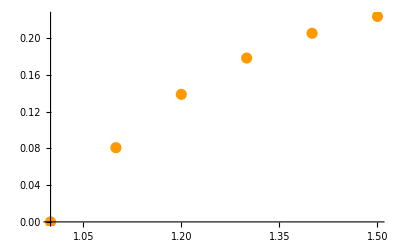

```mathematica
g2Adams=ListPlot[ynumAdams , PlotStyle->{Hue[0.1] , PointSize[0.02]} ]
```

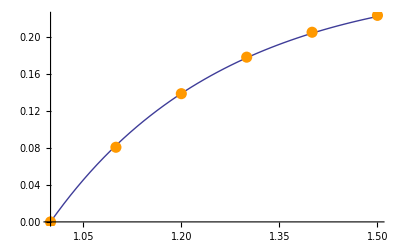

```mathematica
Show[g1,g2Adams]
```